# COVID-19 Data Analysis 경기도

## 장유성 | Yu-Sung Chang CTO, Digital Innovation Group SSG.COM

## Note

## Initialization

```mathematica
ggPageURL="https://www.gg.go.kr/bbs/boardView.do?bsIdx=464&bIdx=2296956&menuId=1535";
```

```mathematica
cacheDirectory=NotebookDirectory[]<>"../data/cache/";
outputDirectory=NotebookDirectory[]<>"../src/output/";
```

## Import Page

```mathematica
raw=Import[ggPageURL,"Data"];
```

```mathematica
tableHeader=raw[[4,2,2,1,2,1]]
```

{연번,확진자,성별,출생연도,확진일자,퇴원,지역}

```mathematica
tableRaw=raw[[4,2,2,1,2,2]];
```

## Data Functions

```mathematica
ggDistrictNames={"군포시","구리시","양평군","고양시","오산시","하남시","시흥시","의왕시","안양시","여주시","안성시","성남시","안산시","용인시","남양주시","김포시","수원시","부천시","과천시","의정부시","이천시","평택시","연천군","가평군","광명시","동두천시","양주시","포천시","화성시","파주시","광주시"};
```

```mathematica
ggDataProcess[body_,eventYear_]:=Module[{
colDate=5,colGen=3,colAge=4,colDistrict=-1,
dates,
genders,
ages,
districts
},
dates=Quiet@DateObject[First@StringCases[ToString[#],RegularExpression["\\d+\\.\\d+"]]]&/@body[[All,colDate]];(* 확진 날자 처리 *)
genders=body[[All,colGen]]; (* 성별 처리 *)
ages=(eventYear-With[{a=ToExpression[StringTake[#,{2,-1}]]},If[a≤20,2000+a,1900+a]])&/@body[[All,colAge]]; (* 나이 처리 *)
districts=(#<>"시"&)/@(StringReplace[#,"("~~__~~")":>""]&/@body[[All,colDistrict]]); (* 출생지 처리: 국적제거 후 "시" 추가 *)

Transpose[{dates,ages,genders,districts}]
]
```

#### Process Raw Data

```mathematica
table=ggDataProcess[tableRaw,2020]; (* 리포트 시점: 2020년 *)
```

#### Define Extract Functions

```mathematica
ggDataColMap={"확진일"->1,"나이"->2,"성별"->3,"거주지"->4};
ggDataColMapR=Reverse[ggDataColMap,1];
ggGetData[col_,range_:All,t_:table]:=t[[range,col/.ggDataColMap]];
```

## Visualization Functions

### VWorld API

```mathematica
vworldAPICred=Import[NotebookDirectory[]<>"../config/config.vworld.key.json","JSON"];
```

```mathematica
vworldAPIURL="http://api.vworld.kr/req/data";
vworldAPIParams={"service"->"data","request"->"GetFeature","data"->"LT_C_ADSIGG_INFO"};
```

```mathematica
vworldAPICall[dist_]:=URLExecute[vworldAPIURL,Join[vworldAPICred,vworldAPIParams,{"attrFilter"->"sig_kor_nm:=:"<>dist}]];
```

### District Coordinates & Centers

```mathematica
Clear[districtCoords]
```

```mathematica
Clear[districtCenter]
```

```mathematica
districtCoords[dist_]:=districtCoords[dist]=Cases[vworldAPICall[dist],HoldPattern["coordinates"->x_]:>x,Infinity][[1,1,1]];
```

```mathematica
districtCenter[dist_]:=districtCenter[dist]=RegionCentroid[Polygon[districtCoords[dist]]]
```

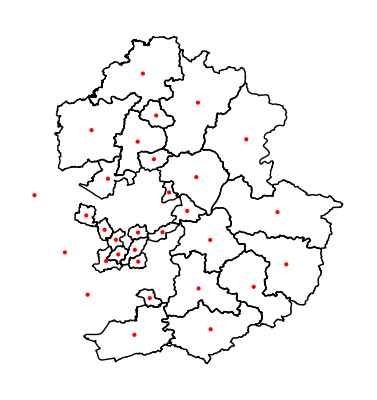

```mathematica
Graphics[{Line/@districtCoords/@ggDistrictNames,Red,Point/@districtCenter/@ggDistrictNames}]
```

#### Color

```mathematica
RGBColor/@(ImageValue[#,{1,1}]&/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}) ;(* Source: Google Calendar colors *)
```

#### Plot Styles

```mathematica
imageWidth=860;
```

```mathematica
legendFrame=(Framed[Style[#,14],Background->GrayLevel[1,.9],FrameStyle->LightGray,RoundingRadius->3]&);
placedLegendFrame=(Placed[#,{Left,Top},legendFrame]&);
```

```mathematica
plotLabelFun[title_]:=Column[{
Style[title,32,GrayLevel[.4]],
Style[
StringReplace[DateString[{"MonthShort","/","DayShort"," (","DayNameShort",") ","Hour24Short","시 현재"}],{"Mon"->"월","Tue"->"화","Wed"->"수","Thu"->"목","Fri"->"금","Sat"->"토","Sun"->"일"}],
20,GrayLevel[.6]]
},Alignment->Center,Spacings->{0,2},BaseStyle->"Label"];
imageDimensions={ImageSize->{imageWidth,Automatic},ImagePadding->{{Automatic,Automatic},{Automatic,20}},AspectRatio->1/2};
```

### District Heatmap

```mathematica
Clear[districtHeatmap]
districtHeatmap[districts_,data_,OptionsPattern[{ImageSize->480,LegendLabel->"Legend",LabelStyle->{FontSize->14,Bold},Min->-1,Max->-1}]]:=
Module[{
min=OptionValue[Min],
max=OptionValue[Max],
imageW=OptionValue[ImageSize],
labelS=OptionValue[LabelStyle],
tally,
regions,
labels,
others
},
tally=Tally[Select[data,MemberQ[districts,#]&]];
others=Complement[districts,tally[[All,1]]];
min=If[min==-1,Min@tally[[All,2]],min];
max=If[max==-1,Max@tally[[All,2]],max];

{regions,labels}=Transpose@(
With[{s=#[[1]],n=#[[2]]},
With[{p=(n-min)/(max-min)},
{
{ColorData["CandyColors",1-p],Polygon[districtCoords[s]]},
Text[Style[Column[{s,Style[n,Smaller,Plain]},Alignment->Center],labelS,GrayLevel[If[p>0.5,1,0.2]]],districtCenter[s]]
}
]
]&/@tally);

Overlay[{
Graphics[{
regions,
GrayLevel[0,0.1],Line/@districtCoords/@districts,
Opacity[1],
labels,
Text[Style[#,labelS,GrayLevel[0.2]],districtCenter[#]]&/@others
},ImageSize->imageW
],
Framed[
Grid[{
{min,
Graphics[
Raster@Reverse[ColorData["CandyColors","Image"][[1,1,1]],2],
ImageSize->{imageW/4,imageW/40},AspectRatio->1/10,PlotRange->{{0,100},{0,1}}],
max},
{"",OptionValue["LegendLabel"],""}
},Alignment->{Center,Center},BaseStyle->{"Text",FontSize->12}],
RoundingRadius->4,FrameStyle->LightGray,FrameMargins->{{5,5},{5,10}}
]
},Alignment->{Right,Top}]
]
```

## Visualization

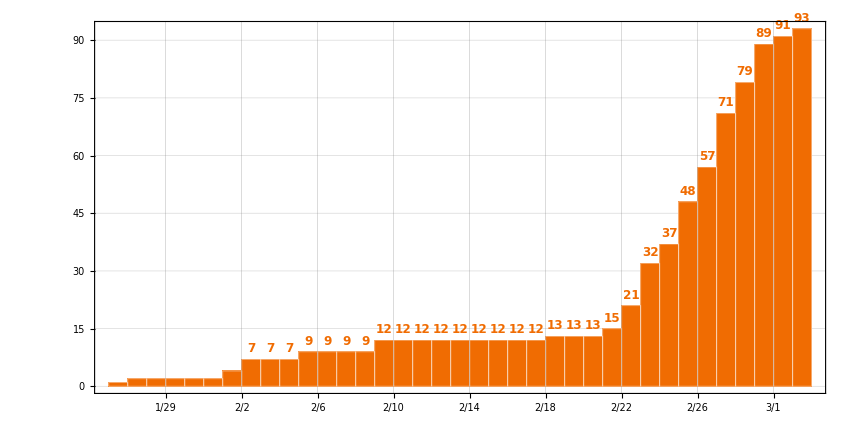
-Graphics-경기도 코로나 19 확진자 현황
3/2 (월) 12시 현재

```mathematica
ggCorona19Growth=Labeled[
DateHistogram[ggGetData["확진일"],"Day","CumulativeCount",
imageDimensions,
Frame->True,
FrameTicksStyle->12,
LabelingFunction->(Placed[Style[If[#>4,#,""],12,Bold,RGBColor[{0.9411764705882353, 0.4235294117647059, 0.00784313725490196, 1.}]],Above]&),
ChartStyle->Directive[{RGBColor[{0.9411764705882353, 0.4235294117647059, 0.00784313725490196, 1.}],EdgeForm[{White,Thick}]}],
GridLines->Automatic,
DateTicksFormat->{"MonthShort","/","DayShort"}],
plotLabelFun["경기도 코로나 19 확진자 현황"],Top]
```

```mathematica
Export[outputDirectory<>"seoul-corona19-growth.svg",SeoulCorona19Growth]
```

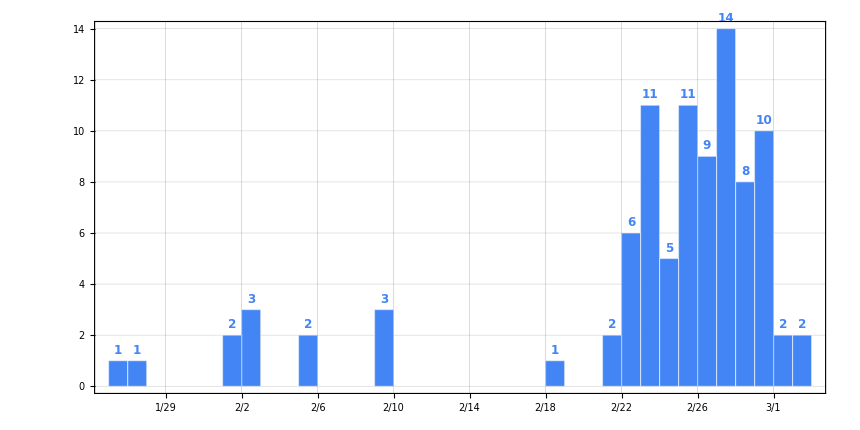
-Graphics-경기도 코로나 19 확진자 증가수
3/2 (월) 12시 현재

```mathematica
ggCorona19Delta=Labeled[
DateHistogram[ggGetData["확진일"],"Day",
imageDimensions,
Frame->True,
FrameTicksStyle->12,
LabelingFunction->(Placed[Style[If[#>0,#,""],12,Bold,RGBColor[{0.2627450980392157, 0.5215686274509804, 0.9607843137254902, 1.}]],Above]&),
ChartStyle->Directive[{RGBColor[{0.2627450980392157, 0.5215686274509804, 0.9607843137254902, 1.}],EdgeForm[{White,Thick}]}],
GridLines->Automatic,
DateTicksFormat->{"MonthShort","/","DayShort"}],
plotLabelFun["경기도 코로나 19 확진자 증가수"],Top]
```

```mathematica
Export[outputDirectory<>"seoul-corona19-delta.svg",SeoulCorona19Delta]
```

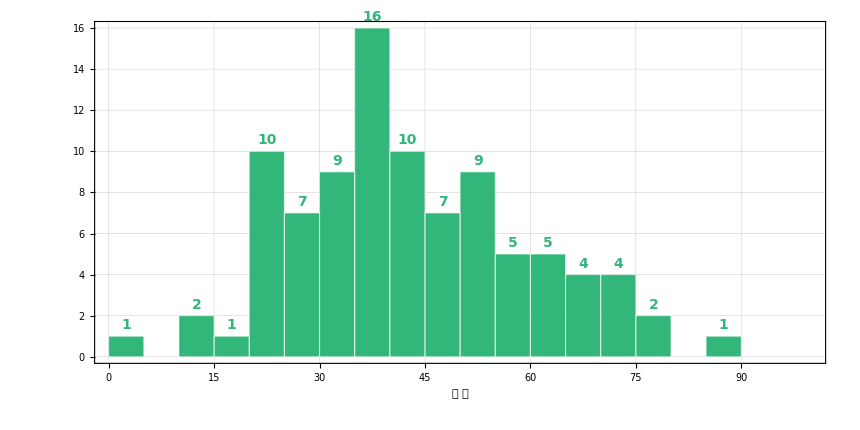
-Graphics-경기도 코로나19 확진자 연령 분포
3/2 (월) 12시 현재

```mathematica
ggCorona19ByAge=Labeled[
Histogram[ggGetData["나이"],{0,100,5},
imageDimensions,
Frame->True,
FrameTicksStyle->12,
FrameLabel->{Style["연 령",12]},
LabelingFunction->(Placed[Style[#,14,RGBColor[{0.19607843137254902, 0.7137254901960784, 0.4745098039215686, 1.}],Bold],Above]&),
ChartStyle->Directive[{RGBColor[{0.19607843137254902, 0.7137254901960784, 0.4745098039215686, 1.}],EdgeForm[{White,Thick}]}],
GridLines->Automatic],
plotLabelFun["경기도 코로나19 확진자 연령 분포"],Top]
```

```mathematica
Export[outputDirectory<>"seoul-corona19-by-age.svg",SeoulCorona19ByAge]
```

```mathematica
ggCorona19ByGender=Labeled[
Pane[
PieChart[Association[Rule@@#&/@Tally[ggGetData["성별"]]],
ImageSize->{Automatic,400},
LabelingFunction->(Placed[Style[#,20,Bold,White],"RadialCenter"]&),
ChartStyle->{RGBColor[{0.9647058823529412, 0.7490196078431373, 0.15294117647058825, 1.}],RGBColor[{0.2627450980392157, 0.5215686274509804, 0.9607843137254902, 1.}]},
ChartLegends->Placed[{"여","남"},Right,Style[#,16,GrayLevel[.3]]&]],
imageDimensions,Alignment->Center
],
plotLabelFun["경기도 코로나19 확진자 성별"],Top]
```

-Graphics-경기도 코로나19 확진자 성별
3/2 (월) 12시 현재

```mathematica
Export[outputDirectory<>"seoul-corona19-by-gender.svg",SeoulCorona19ByGender]
```

## District Visualization

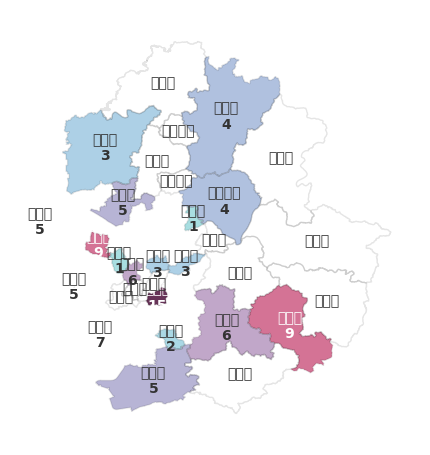
-Graphics-1 | -Graphics- | 15
 | 확 진 자 | 경기도 코로나19 확진자 거주지
3/2 (월) 12시 현재

```mathematica
ggCorona19ByDistricts=Labeled[
Pane[
districtHeatmap[ggDistrictNames,ggGetData["거주지"],ImageSize->imageWidth*.5,LegendLabel->Style["확 진 자",14]],
ImageSize->{imageWidth,Automatic},Alignment->Center],
plotLabelFun["경기도 코로나19 확진자 거주지"],Top]
```

```mathematica
Export[outputDirectory<>"seoul-corona19-by-district.svg",SeoulCorona19ByDistricts]
```

### Animation

```mathematica
filterDates[dateBack_]:=Flatten[Position[seoulGetData["확진일"],x_/;(DatePlus[CurrentDate[],dateBack]>x),1],1]
```

```mathematica
SeoulCorona19ConfirmedDistrictsAni=Manipulate[
SeoulCorona19ConfirmedDistricts=
districtHeatmap[seoulDistrictNames,seoulGetData["거주지",filterDates[n]],ImageSize->imageWidth,LegendLabel->Style["확 진 자",14]],
{n,-30,0,1}];
```

```mathematica
(* Export[outputDirectory<>"seoul-corona19-confirmed-district-ani.gif",SeoulCorona19ConfirmedDistrictsAni,ImageResolution->150] *)
```